```mathematica
Integrate[0.1*a*x^2,{x,0,10}]
```

33.3333 a

```mathematica
Integrate[(x-Integrate[0.1*a*x^2,{x,0,10}])^2,{x,0,10}]
```

333.333-3333.33 a+11111.1 a^2

```mathematica
Integrate[a*x^2,x]
```

(a x^3)/3

```mathematica
f[z_]:=((0.5*z)/(1-0.5*z))^5
```

```mathematica
D[f[ⅇ^z],{z,2}]/.{z->0}
```

110.

```mathematica
f[(1-2*t)^-2.5]
```

0.03125/((1-0.5/(1-2 t)^2.5)^5 (1-2 t)^12.5)

```mathematica
D[(1-2*t)^-2.5,t]/.{t->0}
```

5.

```mathematica
D[(1-2*t)^-2.5,{t,2}]/.{t->0}
```

35.

```mathematica
D[((0.5*z)/(1-0.5*z))^5,z]/(1!)/.{z->0}
```

0.

```mathematica
D[((0.5*z)/(1-0.5*z))^5,z]/(1!)
```

```mathematica
D[((0.5*z)/(1-0.5*z))^5,z]
```

(0.15625 z^4)/(1-0.5 z)^5+(0.078125 z^5)/(1-0.5 z)^6

```mathematica
D[((0.5*z)/(1-0.5*z))^5]
```

(0.03125 z^5)/(1-0.5 z)^5

```mathematica
F[x1_,x2_]:=(x2^2*(√x1)/4)/(√x1+x2^2/4-(x2^2*√x1)/4)
```

```mathematica
Limit[F[x1,x2],x2->Infinity]
```

(√x1)/(1-√x1)

```mathematica
Limit[F[x1,x2],x1->Infinity]
```

-x2^2/(-4+x2^2)

```mathematica
1/(√x1+x2^2/4-(x2^2*√x1)/4)/(x2^2*(√x1)/4)
```

4/(√x1 x2^2 (√x1+x2^2/4-(√x1 x2^2)/4))

```mathematica
MomentGeneratingFunction[]
```

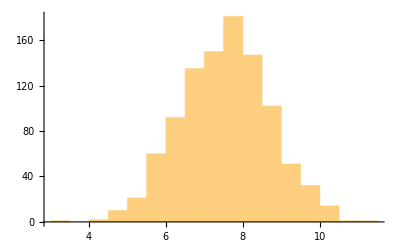

```mathematica
g[p_]:=p*RandomVariate[NormalDistribution[5, 1], 1000]+(1-p)*RandomVariate[NormalDistribution[10, 2], 1000]
Histogram[g[0.5]]
```

```mathematica
k[p_,x_]:=p*(ⅇ^(-(x-5)^2/(2*1^2)))/(√(2 π))+(1-p)*(ⅇ^(-(x-10)^2/(2*2)))/(√(2 π)*√2)
```

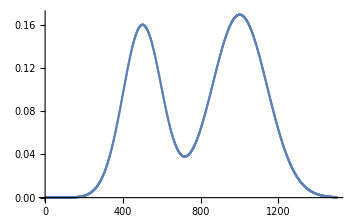

```mathematica
ListPlot[Table[k[0.4,n],{n,0,15,0.01}]]
```

```mathematica
Table[k[0.5,n],{n,0,15,0.01}]
```

{k[0.5,0.],k[0.5,0.01],k[0.5,0.02],k[0.5,0.03],k[0.5,0.04],k[0.5,0.05],k[0.5,0.06],k[0.5,0.07],k[0.5,0.08],k[0.5,0.09],k[0.5,0.1],k[0.5,0.11],k[0.5,0.12],k[0.5,0.13],k[0.5,0.14],k[0.5,0.15],k[0.5,0.16],k[0.5,0.17],k[0.5,0.18],k[0.5,0.19],k[0.5,0.2],k[0.5,0.21],k[0.5,0.22],k[0.5,0.23],k[0.5,0.24],k[0.5,0.25],k[0.5,0.26],k[0.5,0.27],k[0.5,0.28],k[0.5,0.29],k[0.5,0.3],k[0.5,0.31],k[0.5,0.32],k[0.5,0.33],k[0.5,0.34],k[0.5,0.35],k[0.5,0.36],k[0.5,0.37],k[0.5,0.38],k[0.5,0.39],k[0.5,0.4],k[0.5,0.41],k[0.5,0.42],k[0.5,0.43],k[0.5,0.44],k[0.5,0.45],k[0.5,0.46],k[0.5,0.47],k[0.5,0.48],k[0.5,0.49],k[0.5,0.5],k[0.5,0.51],k[0.5,0.52],k[0.5,0.53],k[0.5,0.54],k[0.5,0.55],k[0.5,0.56],k[0.5,0.57],k[0.5,0.58],k[0.5,0.59],k[0.5,0.6],k[0.5,0.61],k[0.5,0.62],k[0.5,0.63],k[0.5,0.64],k[0.5,0.65],k[0.5,0.66],k[0.5,0.67],k[0.5,0.68],k[0.5,0.69],k[0.5,0.7],k[0.5,0.71],k[0.5,0.72],k[0.5,0.73],k[0.5,0.74],k[0.5,0.75],k[0.5,0.76],k[0.5,0.77],k[0.5,0.78],k[0.5,0.79],k[0.5,0.8],k[0.5,0.81],k[0.5,0.82],k[0.5,0.83],k[0.5,0.84],k[0.5,0.85],k[0.5,0.86],k[0.5,0.87],k[0.5,0.88],k[0.5,0.89],k[0.5,0.9],k[0.5,0.91],k[0.5,0.92],k[0.5,0.93],k[0.5,0.94],k[0.5,0.95],k[0.5,0.96],k[0.5,0.97],k[0.5,0.98],k[0.5,0.99],k[0.5,1.],k[0.5,1.01],k[0.5,1.02],k[0.5,1.03],k[0.5,1.04],k[0.5,1.05],k[0.5,1.06],k[0.5,1.07],k[0.5,1.08],k[0.5,1.09],k[0.5,1.1],k[0.5,1.11],k[0.5,1.12],k[0.5,1.13],k[0.5,1.14],k[0.5,1.15],k[0.5,1.16],k[0.5,1.17],k[0.5,1.18],k[0.5,1.19],k[0.5,1.2],k[0.5,1.21],k[0.5,1.22],k[0.5,1.23],k[0.5,1.24],k[0.5,1.25],k[0.5,1.26],k[0.5,1.27],k[0.5,1.28],k[0.5,1.29],k[0.5,1.3],k[0.5,1.31],k[0.5,1.32],k[0.5,1.33],k[0.5,1.34],k[0.5,1.35],k[0.5,1.36],k[0.5,1.37],k[0.5,1.38],k[0.5,1.39],k[0.5,1.4],k[0.5,1.41],k[0.5,1.42],k[0.5,1.43],k[0.5,1.44],k[0.5,1.45],k[0.5,1.46],k[0.5,1.47],k[0.5,1.48],k[0.5,1.49],k[0.5,1.5],k[0.5,1.51],k[0.5,1.52],k[0.5,1.53],k[0.5,1.54],k[0.5,1.55],k[0.5,1.56],k[0.5,1.57],k[0.5,1.58],k[0.5,1.59],k[0.5,1.6],k[0.5,1.61],k[0.5,1.62],k[0.5,1.63],k[0.5,1.64],k[0.5,1.65],k[0.5,1.66],k[0.5,1.67],k[0.5,1.68],k[0.5,1.69],k[0.5,1.7],k[0.5,1.71],k[0.5,1.72],k[0.5,1.73],k[0.5,1.74],k[0.5,1.75],k[0.5,1.76],k[0.5,1.77],k[0.5,1.78],k[0.5,1.79],k[0.5,1.8],k[0.5,1.81],k[0.5,1.82],k[0.5,1.83],k[0.5,1.84],k[0.5,1.85],k[0.5,1.86],k[0.5,1.87],k[0.5,1.88],k[0.5,1.89],k[0.5,1.9],k[0.5,1.91],k[0.5,1.92],k[0.5,1.93],k[0.5,1.94],k[0.5,1.95],k[0.5,1.96],k[0.5,1.97],k[0.5,1.98],k[0.5,1.99],k[0.5,2.],k[0.5,2.01],k[0.5,2.02],k[0.5,2.03],k[0.5,2.04],k[0.5,2.05],k[0.5,2.06],k[0.5,2.07],k[0.5,2.08],k[0.5,2.09],k[0.5,2.1],k[0.5,2.11],k[0.5,2.12],k[0.5,2.13],k[0.5,2.14],k[0.5,2.15],k[0.5,2.16],k[0.5,2.17],k[0.5,2.18],k[0.5,2.19],k[0.5,2.2],k[0.5,2.21],k[0.5,2.22],k[0.5,2.23],k[0.5,2.24],k[0.5,2.25],k[0.5,2.26],k[0.5,2.27],k[0.5,2.28],k[0.5,2.29],k[0.5,2.3],k[0.5,2.31],k[0.5,2.32],k[0.5,2.33],k[0.5,2.34],k[0.5,2.35],k[0.5,2.36],k[0.5,2.37],k[0.5,2.38],k[0.5,2.39],k[0.5,2.4],k[0.5,2.41],k[0.5,2.42],k[0.5,2.43],k[0.5,2.44],k[0.5,2.45],k[0.5,2.46],k[0.5,2.47],k[0.5,2.48],k[0.5,2.49],k[0.5,2.5],k[0.5,2.51],k[0.5,2.52],k[0.5,2.53],k[0.5,2.54],k[0.5,2.55],k[0.5,2.56],k[0.5,2.57],k[0.5,2.58],k[0.5,2.59],k[0.5,2.6],k[0.5,2.61],k[0.5,2.62],k[0.5,2.63],k[0.5,2.64],k[0.5,2.65],k[0.5,2.66],k[0.5,2.67],k[0.5,2.68],k[0.5,2.69],k[0.5,2.7],k[0.5,2.71],k[0.5,2.72],k[0.5,2.73],k[0.5,2.74],k[0.5,2.75],k[0.5,2.76],k[0.5,2.77],k[0.5,2.78],k[0.5,2.79],k[0.5,2.8],k[0.5,2.81],k[0.5,2.82],k[0.5,2.83],k[0.5,2.84],k[0.5,2.85],k[0.5,2.86],k[0.5,2.87],k[0.5,2.88],k[0.5,2.89],k[0.5,2.9],k[0.5,2.91],k[0.5,2.92],k[0.5,2.93],k[0.5,2.94],k[0.5,2.95],k[0.5,2.96],k[0.5,2.97],k[0.5,2.98],k[0.5,2.99],k[0.5,3.],k[0.5,3.01],k[0.5,3.02],k[0.5,3.03],k[0.5,3.04],k[0.5,3.05],k[0.5,3.06],k[0.5,3.07],k[0.5,3.08],k[0.5,3.09],k[0.5,3.1],k[0.5,3.11],k[0.5,3.12],k[0.5,3.13],k[0.5,3.14],k[0.5,3.15],k[0.5,3.16],k[0.5,3.17],k[0.5,3.18],k[0.5,3.19],k[0.5,3.2],k[0.5,3.21],k[0.5,3.22],k[0.5,3.23],k[0.5,3.24],k[0.5,3.25],k[0.5,3.26],k[0.5,3.27],k[0.5,3.28],k[0.5,3.29],k[0.5,3.3],k[0.5,3.31],k[0.5,3.32],k[0.5,3.33],k[0.5,3.34],k[0.5,3.35],k[0.5,3.36],k[0.5,3.37],k[0.5,3.38],k[0.5,3.39],k[0.5,3.4],k[0.5,3.41],k[0.5,3.42],k[0.5,3.43],k[0.5,3.44],k[0.5,3.45],k[0.5,3.46],k[0.5,3.47],k[0.5,3.48],k[0.5,3.49],k[0.5,3.5],k[0.5,3.51],k[0.5,3.52],k[0.5,3.53],k[0.5,3.54],k[0.5,3.55],k[0.5,3.56],k[0.5,3.57],k[0.5,3.58],k[0.5,3.59],k[0.5,3.6],k[0.5,3.61],k[0.5,3.62],k[0.5,3.63],k[0.5,3.64],k[0.5,3.65],k[0.5,3.66],k[0.5,3.67],k[0.5,3.68],k[0.5,3.69],k[0.5,3.7],k[0.5,3.71],k[0.5,3.72],k[0.5,3.73],k[0.5,3.74],k[0.5,3.75],k[0.5,3.76],k[0.5,3.77],k[0.5,3.78],k[0.5,3.79],k[0.5,3.8],k[0.5,3.81],k[0.5,3.82],k[0.5,3.83],k[0.5,3.84],k[0.5,3.85],k[0.5,3.86],k[0.5,3.87],k[0.5,3.88],k[0.5,3.89],k[0.5,3.9],k[0.5,3.91],k[0.5,3.92],k[0.5,3.93],k[0.5,3.94],k[0.5,3.95],k[0.5,3.96],k[0.5,3.97],k[0.5,3.98],k[0.5,3.99],k[0.5,4.],k[0.5,4.01],k[0.5,4.02],k[0.5,4.03],k[0.5,4.04],k[0.5,4.05],k[0.5,4.06],k[0.5,4.07],k[0.5,4.08],k[0.5,4.09],k[0.5,4.1],k[0.5,4.11],k[0.5,4.12],k[0.5,4.13],k[0.5,4.14],k[0.5,4.15],k[0.5,4.16],k[0.5,4.17],k[0.5,4.18],k[0.5,4.19],k[0.5,4.2],k[0.5,4.21],k[0.5,4.22],k[0.5,4.23],k[0.5,4.24],k[0.5,4.25],k[0.5,4.26],k[0.5,4.27],k[0.5,4.28],k[0.5,4.29],k[0.5,4.3],k[0.5,4.31],k[0.5,4.32],k[0.5,4.33],k[0.5,4.34],k[0.5,4.35],k[0.5,4.36],k[0.5,4.37],k[0.5,4.38],k[0.5,4.39],k[0.5,4.4],k[0.5,4.41],k[0.5,4.42],k[0.5,4.43],k[0.5,4.44],k[0.5,4.45],k[0.5,4.46],k[0.5,4.47],k[0.5,4.48],k[0.5,4.49],k[0.5,4.5],k[0.5,4.51],k[0.5,4.52],k[0.5,4.53],k[0.5,4.54],k[0.5,4.55],k[0.5,4.56],k[0.5,4.57],k[0.5,4.58],k[0.5,4.59],k[0.5,4.6],k[0.5,4.61],k[0.5,4.62],k[0.5,4.63],k[0.5,4.64],k[0.5,4.65],k[0.5,4.66],k[0.5,4.67],k[0.5,4.68],k[0.5,4.69],k[0.5,4.7],k[0.5,4.71],k[0.5,4.72],k[0.5,4.73],k[0.5,4.74],k[0.5,4.75],k[0.5,4.76],k[0.5,4.77],k[0.5,4.78],k[0.5,4.79],k[0.5,4.8],k[0.5,4.81],k[0.5,4.82],k[0.5,4.83],k[0.5,4.84],k[0.5,4.85],k[0.5,4.86],k[0.5,4.87],k[0.5,4.88],k[0.5,4.89],k[0.5,4.9],k[0.5,4.91],k[0.5,4.92],k[0.5,4.93],k[0.5,4.94],k[0.5,4.95],k[0.5,4.96],k[0.5,4.97],k[0.5,4.98],k[0.5,4.99],k[0.5,5.],k[0.5,5.01],k[0.5,5.02],k[0.5,5.03],k[0.5,5.04],k[0.5,5.05],k[0.5,5.06],k[0.5,5.07],k[0.5,5.08],k[0.5,5.09],k[0.5,5.1],k[0.5,5.11],k[0.5,5.12],k[0.5,5.13],k[0.5,5.14],k[0.5,5.15],k[0.5,5.16],k[0.5,5.17],k[0.5,5.18],k[0.5,5.19],k[0.5,5.2],k[0.5,5.21],k[0.5,5.22],k[0.5,5.23],k[0.5,5.24],k[0.5,5.25],k[0.5,5.26],k[0.5,5.27],k[0.5,5.28],k[0.5,5.29],k[0.5,5.3],k[0.5,5.31],k[0.5,5.32],k[0.5,5.33],k[0.5,5.34],k[0.5,5.35],k[0.5,5.36],k[0.5,5.37],k[0.5,5.38],k[0.5,5.39],k[0.5,5.4],k[0.5,5.41],k[0.5,5.42],k[0.5,5.43],k[0.5,5.44],k[0.5,5.45],k[0.5,5.46],k[0.5,5.47],k[0.5,5.48],k[0.5,5.49],k[0.5,5.5],k[0.5,5.51],k[0.5,5.52],k[0.5,5.53],k[0.5,5.54],k[0.5,5.55],k[0.5,5.56],k[0.5,5.57],k[0.5,5.58],k[0.5,5.59],k[0.5,5.6],k[0.5,5.61],k[0.5,5.62],k[0.5,5.63],k[0.5,5.64],k[0.5,5.65],k[0.5,5.66],k[0.5,5.67],k[0.5,5.68],k[0.5,5.69],k[0.5,5.7],k[0.5,5.71],k[0.5,5.72],k[0.5,5.73],k[0.5,5.74],k[0.5,5.75],k[0.5,5.76],k[0.5,5.77],k[0.5,5.78],k[0.5,5.79],k[0.5,5.8],k[0.5,5.81],k[0.5,5.82],k[0.5,5.83],k[0.5,5.84],k[0.5,5.85],k[0.5,5.86],k[0.5,5.87],k[0.5,5.88],k[0.5,5.89],k[0.5,5.9],k[0.5,5.91],k[0.5,5.92],k[0.5,5.93],k[0.5,5.94],k[0.5,5.95],k[0.5,5.96],k[0.5,5.97],k[0.5,5.98],k[0.5,5.99],k[0.5,6.],k[0.5,6.01],k[0.5,6.02],k[0.5,6.03],k[0.5,6.04],k[0.5,6.05],k[0.5,6.06],k[0.5,6.07],k[0.5,6.08],k[0.5,6.09],k[0.5,6.1],k[0.5,6.11],k[0.5,6.12],k[0.5,6.13],k[0.5,6.14],k[0.5,6.15],k[0.5,6.16],k[0.5,6.17],k[0.5,6.18],k[0.5,6.19],k[0.5,6.2],k[0.5,6.21],k[0.5,6.22],k[0.5,6.23],k[0.5,6.24],k[0.5,6.25],k[0.5,6.26],k[0.5,6.27],k[0.5,6.28],k[0.5,6.29],k[0.5,6.3],k[0.5,6.31],k[0.5,6.32],k[0.5,6.33],k[0.5,6.34],k[0.5,6.35],k[0.5,6.36],k[0.5,6.37],k[0.5,6.38],k[0.5,6.39],k[0.5,6.4],k[0.5,6.41],k[0.5,6.42],k[0.5,6.43],k[0.5,6.44],k[0.5,6.45],k[0.5,6.46],k[0.5,6.47],k[0.5,6.48],k[0.5,6.49],k[0.5,6.5],k[0.5,6.51],k[0.5,6.52],k[0.5,6.53],k[0.5,6.54],k[0.5,6.55],k[0.5,6.56],k[0.5,6.57],k[0.5,6.58],k[0.5,6.59],k[0.5,6.6],k[0.5,6.61],k[0.5,6.62],k[0.5,6.63],k[0.5,6.64],k[0.5,6.65],k[0.5,6.66],k[0.5,6.67],k[0.5,6.68],k[0.5,6.69],k[0.5,6.7],k[0.5,6.71],k[0.5,6.72],k[0.5,6.73],k[0.5,6.74],k[0.5,6.75],k[0.5,6.76],k[0.5,6.77],k[0.5,6.78],k[0.5,6.79],k[0.5,6.8],k[0.5,6.81],k[0.5,6.82],k[0.5,6.83],k[0.5,6.84],k[0.5,6.85],k[0.5,6.86],k[0.5,6.87],k[0.5,6.88],k[0.5,6.89],k[0.5,6.9],k[0.5,6.91],k[0.5,6.92],k[0.5,6.93],k[0.5,6.94],k[0.5,6.95],k[0.5,6.96],k[0.5,6.97],k[0.5,6.98],k[0.5,6.99],k[0.5,7.],k[0.5,7.01],k[0.5,7.02],k[0.5,7.03],k[0.5,7.04],k[0.5,7.05],k[0.5,7.06],k[0.5,7.07],k[0.5,7.08],k[0.5,7.09],k[0.5,7.1],k[0.5,7.11],k[0.5,7.12],k[0.5,7.13],k[0.5,7.14],k[0.5,7.15],k[0.5,7.16],k[0.5,7.17],k[0.5,7.18],k[0.5,7.19],k[0.5,7.2],k[0.5,7.21],k[0.5,7.22],k[0.5,7.23],k[0.5,7.24],k[0.5,7.25],k[0.5,7.26],k[0.5,7.27],k[0.5,7.28],k[0.5,7.29],k[0.5,7.3],k[0.5,7.31],k[0.5,7.32],k[0.5,7.33],k[0.5,7.34],k[0.5,7.35],k[0.5,7.36],k[0.5,7.37],k[0.5,7.38],k[0.5,7.39],k[0.5,7.4],k[0.5,7.41],k[0.5,7.42],k[0.5,7.43],k[0.5,7.44],k[0.5,7.45],k[0.5,7.46],k[0.5,7.47],k[0.5,7.48],k[0.5,7.49],k[0.5,7.5],k[0.5,7.51],k[0.5,7.52],k[0.5,7.53],k[0.5,7.54],k[0.5,7.55],k[0.5,7.56],k[0.5,7.57],k[0.5,7.58],k[0.5,7.59],k[0.5,7.6],k[0.5,7.61],k[0.5,7.62],k[0.5,7.63],k[0.5,7.64],k[0.5,7.65],k[0.5,7.66],k[0.5,7.67],k[0.5,7.68],k[0.5,7.69],k[0.5,7.7],k[0.5,7.71],k[0.5,7.72],k[0.5,7.73],k[0.5,7.74],k[0.5,7.75],k[0.5,7.76],k[0.5,7.77],k[0.5,7.78],k[0.5,7.79],k[0.5,7.8],k[0.5,7.81],k[0.5,7.82],k[0.5,7.83],k[0.5,7.84],k[0.5,7.85],k[0.5,7.86],k[0.5,7.87],k[0.5,7.88],k[0.5,7.89],k[0.5,7.9],k[0.5,7.91],k[0.5,7.92],k[0.5,7.93],k[0.5,7.94],k[0.5,7.95],k[0.5,7.96],k[0.5,7.97],k[0.5,7.98],k[0.5,7.99],k[0.5,8.],k[0.5,8.01],k[0.5,8.02],k[0.5,8.03],k[0.5,8.04],k[0.5,8.05],k[0.5,8.06],k[0.5,8.07],k[0.5,8.08],k[0.5,8.09],k[0.5,8.1],k[0.5,8.11],k[0.5,8.12],k[0.5,8.13],k[0.5,8.14],k[0.5,8.15],k[0.5,8.16],k[0.5,8.17],k[0.5,8.18],k[0.5,8.19],k[0.5,8.2],k[0.5,8.21],k[0.5,8.22],k[0.5,8.23],k[0.5,8.24],k[0.5,8.25],k[0.5,8.26],k[0.5,8.27],k[0.5,8.28],k[0.5,8.29],k[0.5,8.3],k[0.5,8.31],k[0.5,8.32],k[0.5,8.33],k[0.5,8.34],k[0.5,8.35],k[0.5,8.36],k[0.5,8.37],k[0.5,8.38],k[0.5,8.39],k[0.5,8.4],k[0.5,8.41],k[0.5,8.42],k[0.5,8.43],k[0.5,8.44],k[0.5,8.45],k[0.5,8.46],k[0.5,8.47],k[0.5,8.48],k[0.5,8.49],k[0.5,8.5],k[0.5,8.51],k[0.5,8.52],k[0.5,8.53],k[0.5,8.54],k[0.5,8.55],k[0.5,8.56],k[0.5,8.57],k[0.5,8.58],k[0.5,8.59],k[0.5,8.6],k[0.5,8.61],k[0.5,8.62],k[0.5,8.63],k[0.5,8.64],k[0.5,8.65],k[0.5,8.66],k[0.5,8.67],k[0.5,8.68],k[0.5,8.69],k[0.5,8.7],k[0.5,8.71],k[0.5,8.72],k[0.5,8.73],k[0.5,8.74],k[0.5,8.75],k[0.5,8.76],k[0.5,8.77],k[0.5,8.78],k[0.5,8.79],k[0.5,8.8],k[0.5,8.81],k[0.5,8.82],k[0.5,8.83],k[0.5,8.84],k[0.5,8.85],k[0.5,8.86],k[0.5,8.87],k[0.5,8.88],k[0.5,8.89],k[0.5,8.9],k[0.5,8.91],k[0.5,8.92],k[0.5,8.93],k[0.5,8.94],k[0.5,8.95],k[0.5,8.96],k[0.5,8.97],k[0.5,8.98],k[0.5,8.99],k[0.5,9.],k[0.5,9.01],k[0.5,9.02],k[0.5,9.03],k[0.5,9.04],k[0.5,9.05],k[0.5,9.06],k[0.5,9.07],k[0.5,9.08],k[0.5,9.09],k[0.5,9.1],k[0.5,9.11],k[0.5,9.12],k[0.5,9.13],k[0.5,9.14],k[0.5,9.15],k[0.5,9.16],k[0.5,9.17],k[0.5,9.18],k[0.5,9.19],k[0.5,9.2],k[0.5,9.21],k[0.5,9.22],k[0.5,9.23],k[0.5,9.24],k[0.5,9.25],k[0.5,9.26],k[0.5,9.27],k[0.5,9.28],k[0.5,9.29],k[0.5,9.3],k[0.5,9.31],k[0.5,9.32],k[0.5,9.33],k[0.5,9.34],k[0.5,9.35],k[0.5,9.36],k[0.5,9.37],k[0.5,9.38],k[0.5,9.39],k[0.5,9.4],k[0.5,9.41],k[0.5,9.42],k[0.5,9.43],k[0.5,9.44],k[0.5,9.45],k[0.5,9.46],k[0.5,9.47],k[0.5,9.48],k[0.5,9.49],k[0.5,9.5],k[0.5,9.51],k[0.5,9.52],k[0.5,9.53],k[0.5,9.54],k[0.5,9.55],k[0.5,9.56],k[0.5,9.57],k[0.5,9.58],k[0.5,9.59],k[0.5,9.6],k[0.5,9.61],k[0.5,9.62],k[0.5,9.63],k[0.5,9.64],k[0.5,9.65],k[0.5,9.66],k[0.5,9.67],k[0.5,9.68],k[0.5,9.69],k[0.5,9.7],k[0.5,9.71],k[0.5,9.72],k[0.5,9.73],k[0.5,9.74],k[0.5,9.75],k[0.5,9.76],k[0.5,9.77],k[0.5,9.78],k[0.5,9.79],k[0.5,9.8],k[0.5,9.81],k[0.5,9.82],k[0.5,9.83],k[0.5,9.84],k[0.5,9.85],k[0.5,9.86],k[0.5,9.87],k[0.5,9.88],k[0.5,9.89],k[0.5,9.9],k[0.5,9.91],k[0.5,9.92],k[0.5,9.93],k[0.5,9.94],k[0.5,9.95],k[0.5,9.96],k[0.5,9.97],k[0.5,9.98],k[0.5,9.99],k[0.5,10.],k[0.5,10.01],k[0.5,10.02],k[0.5,10.03],k[0.5,10.04],k[0.5,10.05],k[0.5,10.06],k[0.5,10.07],k[0.5,10.08],k[0.5,10.09],k[0.5,10.1],k[0.5,10.11],k[0.5,10.12],k[0.5,10.13],k[0.5,10.14],k[0.5,10.15],k[0.5,10.16],k[0.5,10.17],k[0.5,10.18],k[0.5,10.19],k[0.5,10.2],k[0.5,10.21],k[0.5,10.22],k[0.5,10.23],k[0.5,10.24],k[0.5,10.25],k[0.5,10.26],k[0.5,10.27],k[0.5,10.28],k[0.5,10.29],k[0.5,10.3],k[0.5,10.31],k[0.5,10.32],k[0.5,10.33],k[0.5,10.34],k[0.5,10.35],k[0.5,10.36],k[0.5,10.37],k[0.5,10.38],k[0.5,10.39],k[0.5,10.4],k[0.5,10.41],k[0.5,10.42],k[0.5,10.43],k[0.5,10.44],k[0.5,10.45],k[0.5,10.46],k[0.5,10.47],k[0.5,10.48],k[0.5,10.49],k[0.5,10.5],k[0.5,10.51],k[0.5,10.52],k[0.5,10.53],k[0.5,10.54],k[0.5,10.55],k[0.5,10.56],k[0.5,10.57],k[0.5,10.58],k[0.5,10.59],k[0.5,10.6],k[0.5,10.61],k[0.5,10.62],k[0.5,10.63],k[0.5,10.64],k[0.5,10.65],k[0.5,10.66],k[0.5,10.67],k[0.5,10.68],k[0.5,10.69],k[0.5,10.7],k[0.5,10.71],k[0.5,10.72],k[0.5,10.73],k[0.5,10.74],k[0.5,10.75],k[0.5,10.76],k[0.5,10.77],k[0.5,10.78],k[0.5,10.79],k[0.5,10.8],k[0.5,10.81],k[0.5,10.82],k[0.5,10.83],k[0.5,10.84],k[0.5,10.85],k[0.5,10.86],k[0.5,10.87],k[0.5,10.88],k[0.5,10.89],k[0.5,10.9],k[0.5,10.91],k[0.5,10.92],k[0.5,10.93],k[0.5,10.94],k[0.5,10.95],k[0.5,10.96],k[0.5,10.97],k[0.5,10.98],k[0.5,10.99],k[0.5,11.],k[0.5,11.01],k[0.5,11.02],k[0.5,11.03],k[0.5,11.04],k[0.5,11.05],k[0.5,11.06],k[0.5,11.07],k[0.5,11.08],k[0.5,11.09],k[0.5,11.1],k[0.5,11.11],k[0.5,11.12],k[0.5,11.13],k[0.5,11.14],k[0.5,11.15],k[0.5,11.16],k[0.5,11.17],k[0.5,11.18],k[0.5,11.19],k[0.5,11.2],k[0.5,11.21],k[0.5,11.22],k[0.5,11.23],k[0.5,11.24],k[0.5,11.25],k[0.5,11.26],k[0.5,11.27],k[0.5,11.28],k[0.5,11.29],k[0.5,11.3],k[0.5,11.31],k[0.5,11.32],k[0.5,11.33],k[0.5,11.34],k[0.5,11.35],k[0.5,11.36],k[0.5,11.37],k[0.5,11.38],k[0.5,11.39],k[0.5,11.4],k[0.5,11.41],k[0.5,11.42],k[0.5,11.43],k[0.5,11.44],k[0.5,11.45],k[0.5,11.46],k[0.5,11.47],k[0.5,11.48],k[0.5,11.49],k[0.5,11.5],k[0.5,11.51],k[0.5,11.52],k[0.5,11.53],k[0.5,11.54],k[0.5,11.55],k[0.5,11.56],k[0.5,11.57],k[0.5,11.58],k[0.5,11.59],k[0.5,11.6],k[0.5,11.61],k[0.5,11.62],k[0.5,11.63],k[0.5,11.64],k[0.5,11.65],k[0.5,11.66],k[0.5,11.67],k[0.5,11.68],k[0.5,11.69],k[0.5,11.7],k[0.5,11.71],k[0.5,11.72],k[0.5,11.73],k[0.5,11.74],k[0.5,11.75],k[0.5,11.76],k[0.5,11.77],k[0.5,11.78],k[0.5,11.79],k[0.5,11.8],k[0.5,11.81],k[0.5,11.82],k[0.5,11.83],k[0.5,11.84],k[0.5,11.85],k[0.5,11.86],k[0.5,11.87],k[0.5,11.88],k[0.5,11.89],k[0.5,11.9],k[0.5,11.91],k[0.5,11.92],k[0.5,11.93],k[0.5,11.94],k[0.5,11.95],k[0.5,11.96],k[0.5,11.97],k[0.5,11.98],k[0.5,11.99],k[0.5,12.],k[0.5,12.01],k[0.5,12.02],k[0.5,12.03],k[0.5,12.04],k[0.5,12.05],k[0.5,12.06],k[0.5,12.07],k[0.5,12.08],k[0.5,12.09],k[0.5,12.1],k[0.5,12.11],k[0.5,12.12],k[0.5,12.13],k[0.5,12.14],k[0.5,12.15],k[0.5,12.16],k[0.5,12.17],k[0.5,12.18],k[0.5,12.19],k[0.5,12.2],k[0.5,12.21],k[0.5,12.22],k[0.5,12.23],k[0.5,12.24],k[0.5,12.25],k[0.5,12.26],k[0.5,12.27],k[0.5,12.28],k[0.5,12.29],k[0.5,12.3],k[0.5,12.31],k[0.5,12.32],k[0.5,12.33],k[0.5,12.34],k[0.5,12.35],k[0.5,12.36],k[0.5,12.37],k[0.5,12.38],k[0.5,12.39],k[0.5,12.4],k[0.5,12.41],k[0.5,12.42],k[0.5,12.43],k[0.5,12.44],k[0.5,12.45],k[0.5,12.46],k[0.5,12.47],k[0.5,12.48],k[0.5,12.49],k[0.5,12.5],k[0.5,12.51],k[0.5,12.52],k[0.5,12.53],k[0.5,12.54],k[0.5,12.55],k[0.5,12.56],k[0.5,12.57],k[0.5,12.58],k[0.5,12.59],k[0.5,12.6],k[0.5,12.61],k[0.5,12.62],k[0.5,12.63],k[0.5,12.64],k[0.5,12.65],k[0.5,12.66],k[0.5,12.67],k[0.5,12.68],k[0.5,12.69],k[0.5,12.7],k[0.5,12.71],k[0.5,12.72],k[0.5,12.73],k[0.5,12.74],k[0.5,12.75],k[0.5,12.76],k[0.5,12.77],k[0.5,12.78],k[0.5,12.79],k[0.5,12.8],k[0.5,12.81],k[0.5,12.82],k[0.5,12.83],k[0.5,12.84],k[0.5,12.85],k[0.5,12.86],k[0.5,12.87],k[0.5,12.88],k[0.5,12.89],k[0.5,12.9],k[0.5,12.91],k[0.5,12.92],k[0.5,12.93],k[0.5,12.94],k[0.5,12.95],k[0.5,12.96],k[0.5,12.97],k[0.5,12.98],k[0.5,12.99],k[0.5,13.],k[0.5,13.01],k[0.5,13.02],k[0.5,13.03],k[0.5,13.04],k[0.5,13.05],k[0.5,13.06],k[0.5,13.07],k[0.5,13.08],k[0.5,13.09],k[0.5,13.1],k[0.5,13.11],k[0.5,13.12],k[0.5,13.13],k[0.5,13.14],k[0.5,13.15],k[0.5,13.16],k[0.5,13.17],k[0.5,13.18],k[0.5,13.19],k[0.5,13.2],k[0.5,13.21],k[0.5,13.22],k[0.5,13.23],k[0.5,13.24],k[0.5,13.25],k[0.5,13.26],k[0.5,13.27],k[0.5,13.28],k[0.5,13.29],k[0.5,13.3],k[0.5,13.31],k[0.5,13.32],k[0.5,13.33],k[0.5,13.34],k[0.5,13.35],k[0.5,13.36],k[0.5,13.37],k[0.5,13.38],k[0.5,13.39],k[0.5,13.4],k[0.5,13.41],k[0.5,13.42],k[0.5,13.43],k[0.5,13.44],k[0.5,13.45],k[0.5,13.46],k[0.5,13.47],k[0.5,13.48],k[0.5,13.49],k[0.5,13.5],k[0.5,13.51],k[0.5,13.52],k[0.5,13.53],k[0.5,13.54],k[0.5,13.55],k[0.5,13.56],k[0.5,13.57],k[0.5,13.58],k[0.5,13.59],k[0.5,13.6],k[0.5,13.61],k[0.5,13.62],k[0.5,13.63],k[0.5,13.64],k[0.5,13.65],k[0.5,13.66],k[0.5,13.67],k[0.5,13.68],k[0.5,13.69],k[0.5,13.7],k[0.5,13.71],k[0.5,13.72],k[0.5,13.73],k[0.5,13.74],k[0.5,13.75],k[0.5,13.76],k[0.5,13.77],k[0.5,13.78],k[0.5,13.79],k[0.5,13.8],k[0.5,13.81],k[0.5,13.82],k[0.5,13.83],k[0.5,13.84],k[0.5,13.85],k[0.5,13.86],k[0.5,13.87],k[0.5,13.88],k[0.5,13.89],k[0.5,13.9],k[0.5,13.91],k[0.5,13.92],k[0.5,13.93],k[0.5,13.94],k[0.5,13.95],k[0.5,13.96],k[0.5,13.97],k[0.5,13.98],k[0.5,13.99],k[0.5,14.],k[0.5,14.01],k[0.5,14.02],k[0.5,14.03],k[0.5,14.04],k[0.5,14.05],k[0.5,14.06],k[0.5,14.07],k[0.5,14.08],k[0.5,14.09],k[0.5,14.1],k[0.5,14.11],k[0.5,14.12],k[0.5,14.13],k[0.5,14.14],k[0.5,14.15],k[0.5,14.16],k[0.5,14.17],k[0.5,14.18],k[0.5,14.19],k[0.5,14.2],k[0.5,14.21],k[0.5,14.22],k[0.5,14.23],k[0.5,14.24],k[0.5,14.25],k[0.5,14.26],k[0.5,14.27],k[0.5,14.28],k[0.5,14.29],k[0.5,14.3],k[0.5,14.31],k[0.5,14.32],k[0.5,14.33],k[0.5,14.34],k[0.5,14.35],k[0.5,14.36],k[0.5,14.37],k[0.5,14.38],k[0.5,14.39],k[0.5,14.4],k[0.5,14.41],k[0.5,14.42],k[0.5,14.43],k[0.5,14.44],k[0.5,14.45],k[0.5,14.46],k[0.5,14.47],k[0.5,14.48],k[0.5,14.49],k[0.5,14.5],k[0.5,14.51],k[0.5,14.52],k[0.5,14.53],k[0.5,14.54],k[0.5,14.55],k[0.5,14.56],k[0.5,14.57],k[0.5,14.58],k[0.5,14.59],k[0.5,14.6],k[0.5,14.61],k[0.5,14.62],k[0.5,14.63],k[0.5,14.64],k[0.5,14.65],k[0.5,14.66],k[0.5,14.67],k[0.5,14.68],k[0.5,14.69],k[0.5,14.7],k[0.5,14.71],k[0.5,14.72],k[0.5,14.73],k[0.5,14.74],k[0.5,14.75],k[0.5,14.76],k[0.5,14.77],k[0.5,14.78],k[0.5,14.79],k[0.5,14.8],k[0.5,14.81],k[0.5,14.82],k[0.5,14.83],k[0.5,14.84],k[0.5,14.85],k[0.5,14.86],k[0.5,14.87],k[0.5,14.88],k[0.5,14.89],k[0.5,14.9],k[0.5,14.91],k[0.5,14.92],k[0.5,14.93],k[0.5,14.94],k[0.5,14.95],k[0.5,14.96],k[0.5,14.97],k[0.5,14.98],k[0.5,14.99],k[0.5,15.]}